```mathematica
EE[A_Symbol,S_Symbol,Θ_]:=-S''[Θ]+1/Sin[Θ] A'[Θ]-2 Cos[Θ]/Sin[Θ] S'[Θ]+S[Θ]
BB[A_Symbol,S_Symbol,Θ_]:=-A''[Θ]+1/Sin[Θ] S'[Θ]-2 Cos[Θ]/Sin[Θ] A'[Θ]+A[Θ]
```

```mathematica
Coeff[l_,QQ_Symbol]:=1/(2l+1)Integrate[Sin[Θ]LegendreP[l,Cos[Θ]]QQ[Θ],{Θ,0,π}]
```

```mathematica
CoeffD[l_,QQ_Symbol]:=1/(2l+1)2^l Sum[Binomial[l,k]Binomial[1/2(l+k-1),l]Integrate[Sin[Θ] Cos[Θ]^k QQ[Θ],{Θ,0,π}],{k,0,l}]
```

## Transverse Traceless (Tensorial)

```mathematica
AlphaTT[Θ_]:=(2π)/3-(14π)/3 Sin[Θ/2]^2-8π Sin[Θ/2]^4/(1-Sin[Θ/2]^2)Log[Sin[Θ/2]];
SigmaTT[Θ_]:=(2π)/3-(14π)/3 Sin[Θ/2]^2-8π Sin[Θ/2]^4/(1-Sin[Θ/2]^2)Log[Sin[Θ/2]];
```

```mathematica
EE[AlphaTT,SigmaTT,Θ]//FullSimplify
```

4/3 π (3+Cos[Θ]-12 (-1+Cos[Θ]) Log[Sin[Θ/2]])

```mathematica
EEBBTT[Θ_]:=(16π)/3-(8π)/3 Sin[Θ/2]^2+32π Sin[Θ/2]^2 Log[Sin[Θ/2]];
```

```mathematica
(4π)/3 Integrate[x^k(3+x),{x,-1,1},Assumptions->{k∈Integers,k≥0}]+8π Integrate[x^k(1-x) Log[(1-x)/2],{x,-1,1},Assumptions->{k∈Integers,k≥0}]
```

4/3 ((3 (1+(-1)^k))/(1+k)+(1+(-1)^(1+k))/(2+k)) π-(8 π (-1+ⅇ^(ⅈ k π)+2 (2+k) HypergeometricPFQ[{1,1,-1-k},{2,2},2]))/((1+k) (2+k))

```mathematica
CoeffGRE[l_]:=(2^l 4π)/(3(2l+1))Sum[Binomial[l,k]Binomial[1/2(l+k-1),l](13+4 k+(-1)^k (-1+2 k)-12 (2+k) HypergeometricPFQ[{1,1,-1-k},{2,2},2])/((1+k) (2+k)),{k,0,l}]
```

```mathematica
CoeffTTE=Table[{l,√2 CoeffGRE[l]},{l,1,100}]//N;
```

```mathematica
Export["coeffs.dat",CoeffTTE]
```

coeffs.dat

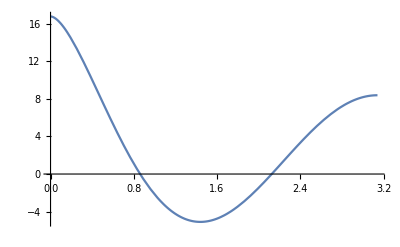

```mathematica
Plot[EEBBTT[Θ],{Θ,0,π}]
```

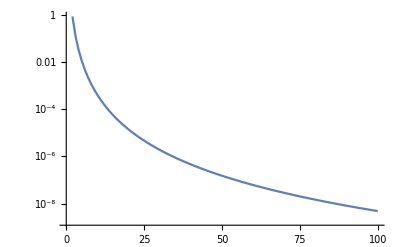

```mathematica
ListLogPlot[CoeffTTE,PlotRange->All,Joined->True]
```

## Scalar Transverse

```mathematica
AlphaST[Θ_]:=π/3;
SigmaST[Θ_]:=π/3 Cos[Θ];
```

```mathematica
EEST[Θ_]:=4/3 π Cos[Θ];
BBST[Θ_]:=0;
```

```mathematica
CoeffSTE=Table[{l,Coeff[l,EEST]},{l,0,10}]
CoeffSTB=Table[{l,Coeff[l,BBST]},{l,0,10}];
```

{{0,0},{1,(8 π)/27},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0}}

```mathematica
CoeffSE[l_]:=(2^l 4 π)/(3(2l+1))Sum[Binomial[l,k]Binomial[1/2(l+k-1),l](1+(-1)^(1+k))/(2+k),{k,0,l}]
```

```mathematica
CoeffsS=Table[{l,CoeffSE[l]},{l,0,10}]//N
```

{{0.,0.},{1.,0.930842},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.}}

```mathematica
Export["coeffs.dat",CoeffsS]
```

coeffs.dat

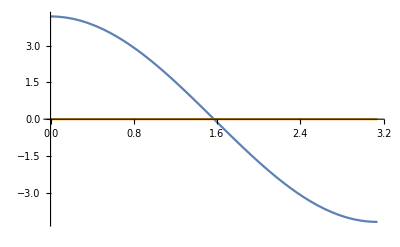

```mathematica
Plot[{EEST[Θ],BBST[Θ]},{Θ,0,π}]
```

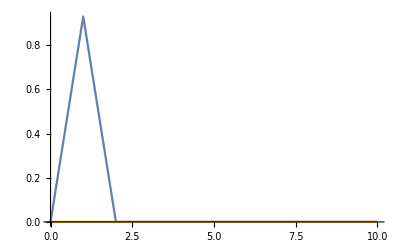

```mathematica
ListPlot[{CoeffSTE,CoeffSTB},PlotRange->All,Joined->True]
```

## Vectorial Longitudinal

```mathematica
AlphaVectorial[Θ_]:=(4π)/3+(8π)/3 Sin[Θ/2]^2+8π Sin[Θ/2]^2/(1-Sin[Θ/2]^2)Log[Sin[Θ/2]];
SigmaVectorial[Θ_]:=(4π)/3+(8π)/3 Sin[Θ/2]^2+8π Sin[Θ/2]^2/(1-Sin[Θ/2]^2)Log[Sin[Θ/2]];
```

```mathematica
EE[AlphaVectorial,SigmaVectorial,Θ]//FullSimplify
```

-4/3 π (3+4 Cos[Θ]+6 Log[Sin[Θ/2]])

```mathematica
EEBBVectorial[Θ_]:=-(28π)/3+(32π)/3 Sin[Θ/2]^2-8π Log[Sin[Θ/2]];
```

```mathematica
CoeffVE[l_]:=4/3 π 1/(2l+1)2^l Sum[Binomial[l,k]Binomial[1/2(l+k-1),l] 1/((1+k) (2+k))(-10-7 k+3 (2+k) HarmonicNumber[1+k]+(-1)^k (-2+k+3 (2+k) LerchPhi[-1,1,2+k])+k Log[8]+Log[64]),{k,0,l}]
```

```mathematica
CoeffVectorialE=Table[{l,N[√2 CoeffVE[l]//FullSimplify]},{l,1,100}]
```

{{1,0.658205},{2,1.18477},{3,0.423132},{4,0.197461},{5,0.107706},{6,0.0650972},{7,0.0423132},{8,0.0290385},{9,0.0207854},{10,0.0153866},{11,0.0117072},{12,0.00911361},{13,0.00723302},{14,0.0058363},{15,0.00477729},{16,0.00395979},{17,0.00331868},{18,0.00280884},{19,0.00239832},{20,0.00206406},{21,0.00178914},{22,0.00156096},{23,0.00136999},{24,0.00120895},{25,0.00107219},{26,0.000955305},{27,0.000854812},{28,0.000767934},{29,0.000692442},{30,0.00062653},{31,0.000568725},{32,0.000517819},{33,0.000472811},{34,0.000432871},{35,0.000397307},{36,0.000365534},{37,0.000337061},{38,0.00031147},{39,0.000288405},{40,0.000267563},{41,0.000248682},{42,0.000231536},{43,0.000215931},{44,0.000201697},{45,0.000188687},{46,0.000176773},{47,0.000165841},{48,0.000155792},{49,0.000146539},{50,0.000138005},{51,0.00013012},{52,0.000122825},{53,0.000116065},{54,0.000109792},{55,0.000103964},{56,0.0000985402},{57,0.0000934876},{58,0.0000887747},{59,0.0000843732},{60,0.000080258},{61,0.0000764061},{62,0.0000727969},{63,0.0000694114},{64,0.0000662326},{65,0.000063245},{66,0.0000604344},{67,0.000057788},{68,0.0000552938},{69,0.0000529411},{70,0.00005072},{71,0.0000486215},{72,0.0000466371},{73,0.0000447593},{74,0.0000429809},{75,0.0000412955},{76,0.0000396971},{77,0.0000381802},{78,0.0000367395},{79,0.0000353705},{80,0.0000340686},{81,0.0000328298},{82,0.0000316504},{83,0.0000305268},{84,0.0000294557},{85,0.0000284342},{86,0.0000274594},{87,0.0000265286},{88,0.0000256395},{89,0.0000247896},{90,0.0000239769},{91,0.0000231993},{92,0.000022455},{93,0.0000217421},{94,0.0000210592},{95,0.0000204045},{96,0.0000197767},{97,0.0000191744},{98,0.0000185963},{99,0.0000180412},{100,0.000017508}}

```mathematica
Export["coeffs.dat",CoeffVectorialE]
```

coeffs.dat

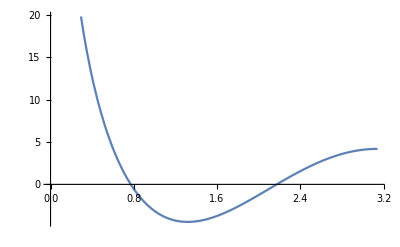

```mathematica
Plot[EEBBVectorial[Θ],{Θ,0,π}]
```

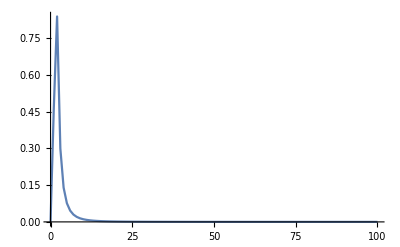

```mathematica
ListPlot[CoeffVectorialE,PlotRange->All,Joined->True]
```

## Scalar Longitudinal

```mathematica
AlphaLongitudinal[Θ_]:=-(4π)/3-2π 1/(1-Sin[Θ/2]^2)Log[Sin[Θ/2]];
SigmaLongitudinal[Θ_]:=-(10π)/3+(8π)/3 Sin[Θ/2]^2-2π 1/(1-Sin[Θ/2]^2)Log[Sin[Θ/2]];
```

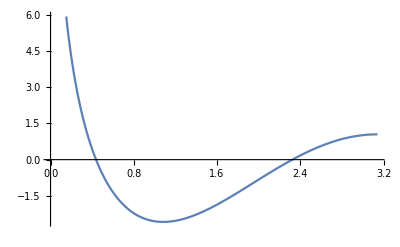

```mathematica
Plot[SigmaLongitudinal[Θ],{Θ,0,π}]
```

```mathematica
EELongitudinal[Θ_]:=-2/3 π (3+8 Cos[Θ]);
BBLongitudinal[Θ_]:=0;
```

```mathematica
CoeffLE[l_]:=-1/(2l+1)2^l Sum[Binomial[l,k]Binomial[1/2(l+k-1),l](2 (14+11 k+(-1)^(1+k) (2+5 k)) π)/(3 (1+k) (2+k)),{k,0,l}]
```

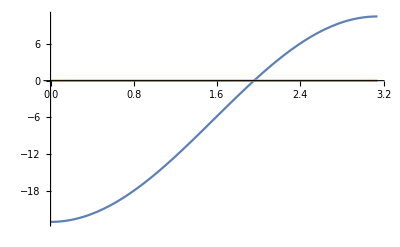

```mathematica
Plot[{EELongitudinal[Θ],BBLongitudinal[Θ]},{Θ,0,π}]
```

```mathematica
CoeffLongitudinalE=Table[{l,CoeffLE[l]},{l,0,10}]
```

{{0,-4 π},{1,-(32 π)/27},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0}}

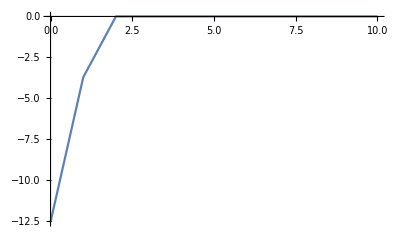

```mathematica
ListPlot[CoeffLongitudinalE,PlotRange->All,Joined->True]
```